```mathematica
a=6.4;
primvecs=.5 a{{0,1,1},{1,0,1},{1,1,0}}
```

{{0.,3.2,3.2},{3.2,0.,3.2},{3.2,3.2,0.}}

```mathematica
arrow[point_]:=Arrow[{{0,0,0},point}]
```

```mathematica
plot1=Graphics3D[Table[arrow[primvecs[[i]]],{i,3}]];
```

-Graphics3D-

```mathematica
reciprocalVectors[primitiveVectors_]:=
(
a1=primitiveVectors[[1]];
a2=primitiveVectors[[2]];
a3=primitiveVectors[[3]];
2π{Cross[a2,a3]/(a1.Cross[a2,a3]),Cross[a3,a1]/(a2.Cross[a3,a1]),Cross[a1,a2]/(a3.Cross[a1,a2])}
)
```

```mathematica
(2π)/a
```

0.981748

```mathematica
reciprocalVectors[primvecs]
```

{{-0.981748,0.981748,0.981748},{0.981748,-0.981748,0.981748},{0.981748,0.981748,-0.981748}}

```mathematica
Graphics3D[Table[arrow[reciprocalVectors[primvecs][[i]]],{i,3}]]
```

-Graphics3D-

```mathematica
reciprocal=(2π)/a{{1,0},{0,1}};
```

```mathematica
kPath[t_]:=Piecewise[{{.5reciprocal[[1]] t,0≤ t≤ 1},{.5reciprocal[[1]]+(.5reciprocal[[2]])(t-1),1≤ t≤2},{.5reciprocal[[1]]+.5reciprocal[[2]]-(.5reciprocal[[1]]+.5reciprocal[[2]])(t-2),2≤ t≤3}}]
```

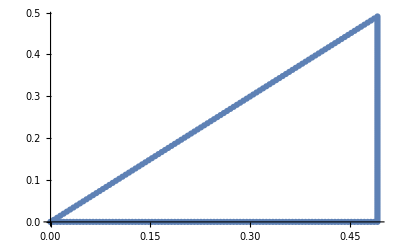

```mathematica
ListPlot@Table[kPath[i],{i,0,3,0.01}]
```